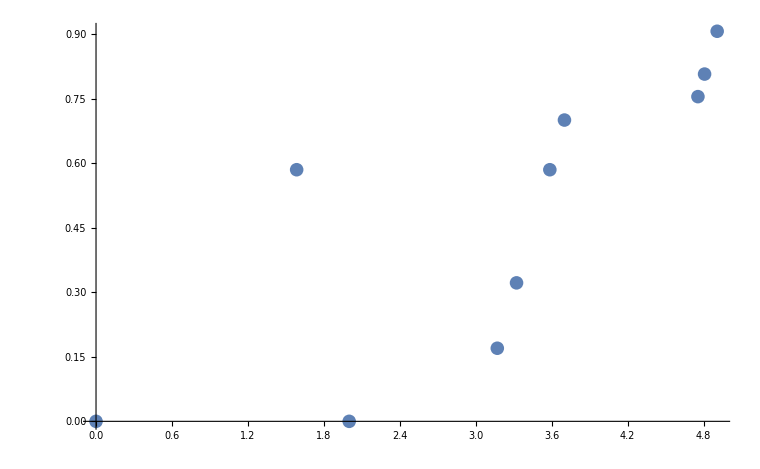

```mathematica
ListPlot[Table[
With[
{n=FromDigits[IntegerDigits[k,2],3]},
{N[Log[2,n]],N[Log[2,n]]-Floor[N[Log[2,n]]]}]
,{k,1,10}]
]
```

```mathematica
2^8
```

256

```mathematica
,
PlotRange->{Automatic,{0,0.1}}
```

```mathematica
3^n=
```

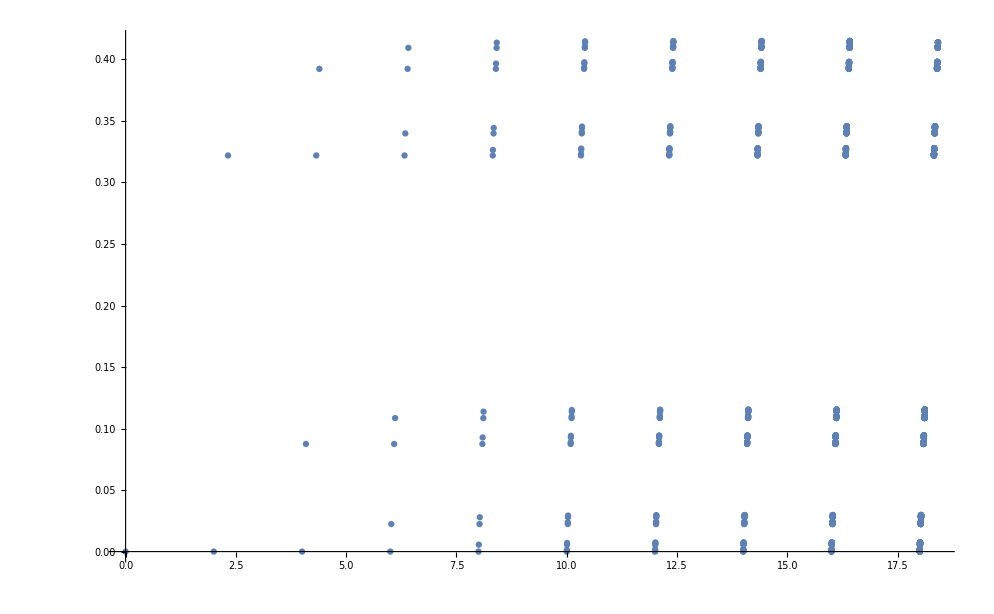

```mathematica
ListPlot[Table[
With[
{n=FromDigits[IntegerDigits[k,2],4]},
{N[Log[2,n]],N[Log[2,n]]-Floor[N[Log[2,n]]]}]
,{k,1,1000}]
]
```

```mathematica
Select[
Monitor  [
Table[
With[
{n=FromDigits[IntegerDigits[k,2],3]},
n]
,{k,1,10000}],
k],
N[Log[2,#]]-Floor[N[Log[2,#]]]==0&]
```

{1,4,256}

```mathematica
Select[
Monitor  [
Table[
With[
{n=FromDigits[IntegerDigits[k,2],4]},
n]
,{k,1,10000}],
k],
N[Log[2,#]]-Floor[N[Log[2,#]]]==0&]
```

{1,4,16,64,256,1024,4096,16384,65536,262144,1048576,4194304,16777216,67108864}

```mathematica
Select[
Monitor  [
Table[
With[
{n=FromDigits[IntegerDigits[k,2],5]},
n]
,{k,1,1000000}],
k],
N[Log[2,#]]-Floor[N[Log[2,#]]]==0&]
```

{1}

```mathematica
Select[
Monitor  [
Table[
With[
{n=FromDigits[IntegerDigits[k,2],6]},
n]
,{k,1,1000000}],
k],
N[Log[2,#]]-Floor[N[Log[2,#]]]==0&]
```

{1}

```mathematica
Select[
Monitor  [
Table[
With[
{n=FromDigits[IntegerDigits[k,2],7]},
n]
,{k,1,1000000}],
k],
N[Log[2,#]]-Floor[N[Log[2,#]]]==0&]
```

{1,8}